```mathematica
n=5;
CirclePoints[1,n]
```

{{√(5/8-(√5)/8),1/4 (-1-√5)},{√(5/8+(√5)/8),1/4 (-1+√5)},{0,1},{-√(5/8+(√5)/8),1/4 (-1+√5)},{-√(5/8-(√5)/8),1/4 (-1-√5)}}

```mathematica
Point[{{√(5/8-(√5)/8),1/4 (-1-√5)},{√(5/8+(√5)/8),1/4 (-1+√5)},{0,1},{-√(5/8+(√5)/8),1/4 (-1+√5)},{-√(5/8-(√5)/8),1/4 (-1-√5)}}]
```

Point[{{√(5/8-(√5)/8),1/4 (-1-√5)},{√(5/8+(√5)/8),1/4 (-1+√5)},{0,1},{-√(5/8+(√5)/8),1/4 (-1+√5)},{-√(5/8-(√5)/8),1/4 (-1-√5)}}]

```mathematica
Graphics@Point[{{√(5/8-(√5)/8),1/4 (-1-√5)},{√(5/8+(√5)/8),1/4 (-1+√5)},{0,1},{-√(5/8+(√5)/8),1/4 (-1+√5)},{-√(5/8-(√5)/8),1/4 (-1-√5)}}]
```

-Graphics-

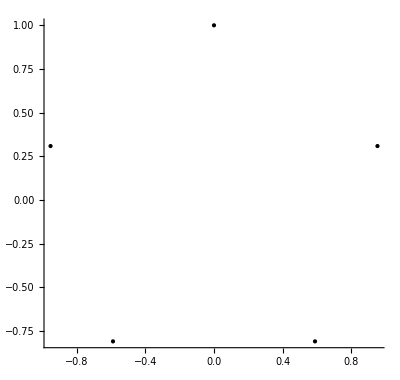

```mathematica
Show[Graphics[Point[{{√(5/8-(√5)/8),1/4 (-1-√5)},{√(5/8+(√5)/8),1/4 (-1+√5)},{0,1},{-√(5/8+(√5)/8),1/4 (-1+√5)},{-√(5/8-(√5)/8),1/4 (-1-√5)}}]],Axes->True,AxesStyle->Gray]
```

```mathematica
Cos[2/17Pi]
```

Cos[(2 π)/17]

```mathematica
ToRadicals[Sin[π/17]]
```

1/4 √(8-√(2 (15+√17-√(2 (17-√17))+√(2 (34+6 √17+√(2 (17-√17))-√(34 (17-√17))+8 √(2 (17+√17)))))))

Root0.0122Root[257-2829056 #1^2+9341542912 #1^4-14684905457664 #1^6+«180»+76590530424347007901344806703644554838724914510427731032401903224398192054370304000 #1^248-4940852066259070724854880916913994549596150660369903668831281342667153489021370368 #1^250+236208625038547706401870836231160289026429939343865148105241005277142289894866944 #1^252-7439641733497565555964435786808198079572596514767406239535149772508418579365888 #1^254+115792089237316195423570985008687907853269984665640564039457584007913129639936 #1^256&,129]0.012223791492543134

```mathematica
ToRadicals[Sin[π/5]]
```

√(5/8-(√5)/8)

```mathematica
RootReduce[-1/2 (-1)^(256/257) (1+(-1)^(2/257))]
```

Root1.00Root[1+128 #1-8320 #1^2-349440 #1^3+11531520 #1^4+285981696 #1^5-6386924544 #1^6-111314970624 #1^7+«169»+824451005929602500336840521524763162574848 #1^121-1689448782642628074460738773616317956096000 #1^122-82412135738664784120036037737381363712000 #1^123+167482727468899399985879689595323416576000 #1^124+5359447279004780799548150067050349330432 #1^125-10803965149739796214962143785958640713728 #1^126-170141183460469231731687303715884105728 #1^127+340282366920938463463374607431768211456 #1^128&,128]0.9999252866697326

```mathematica
N[%307]
```

0.999925

```mathematica
f[x_,y_,z_]=(x+y+z-x y z)/(1-x y-y z-z x)
```

(x+y+z-x y z)/(1-x y-x z-y z)

{{1,4},{7,2},{10,3}}

{26/43,3/5}

{26/43,3/5}

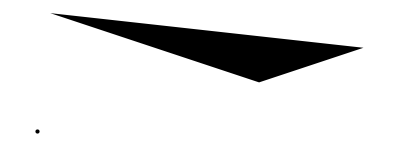

```mathematica
ps=RandomInteger[{1,10},{3,2}]
px=Thread[f@@ps]
px=MapThread[f,ps]
Graphics[{Polygon[ps],Point[px]}]
```

```mathematica
{1.8638885115321988,-7.105236218688421}
```

{1.86389,-7.10524}